```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\sam\Documents\GitHub\samuelpmish.github.io\notes\RocketLeague

```mathematica
vmax[κ_]:= Interpolation[({{0.0069, 10}, {0.00398, 500}, {0.00235, 1000}, {0.001375, 1500}, {0.0011, 1750}, {0.00088, 2300}}), InterpolationOrder->1][Clip[Abs[κ], {0.00088, 0.0069}]]
```

```mathematica
scale = 300;
P0={0,0};
P1={2,0.5};
P2={2,4};
P3={4,2};
g[t_] := Table[BernsteinBasis[3, i, t], {i, 0, 3}].{P0, P1, P2, P3}scale
κ[t_] := Det[{g'[t], g''[t]}]/(Norm[g'[t]])^3
s = Interpolation[Table[{T, NIntegrate[Norm[g'[t]], {t,0, T}]}, {T, 0, 1, 0.005}]];
```

```mathematica
svalues = Table[NIntegrate[Norm[g'[t]], {t,0, T}], {T, 0, 1, 0.005}]
```

{0.,9.25019,18.4487,27.5984,36.702,45.7622,54.7817,63.763,72.7087,81.6212,90.5027,99.3557,108.182,116.984,173,1446.52,1456.51,1466.7,1477.09,1487.69,1498.5,1509.52,1520.77,1532.23,1543.91,1555.82,1567.96,1580.34,1592.95}
 |  |  |  |

```mathematica
sinv =  Interpolation[Table[{NIntegrate[Norm[g'[t]], {t,0, T}],T}, {T, 0, 1, 0.005}]];
```

```mathematica
speedlimits = Table[{s[t], vmax[κ[t]]}, {t, 0, 1, 0.005}];
```

```mathematica
Interpolation[speedlimits][d[x tmax]]
```

InterpolatingFunction[…][d[tmax x]]

```mathematica
frames = Table[
τ = sinv[d[x tmax]];
GraphicsColumn[{
Graphics[{
Black,
Line[Table[g[t], {t, 0, 1, 0.01}]],
PointSize[0.02],
Point[g[τ]]
}, PlotRange->scale{{-1, 5}, {-1, 3.5}}, ImageSize->640],
Show[
ListLinePlot[speedlimits, AxesLabel->{"s", "v(s)"}, LabelStyle->Large],
Graphics[{
PointSize[0.02],
Point[{d[x tmax], Interpolation[speedlimits][d[x tmax]]}]
}]
]
}],
{x, 0, 1, 0.005}
];
```

```mathematica
Do[
Export[ToString[i]<>".png", frames[[i]]]
,
{i, 1, Length[frames]}
];
```

```mathematica
ListAnimate[frames]
```

```mathematica
frames = Table[
τ = sinv[d[Min[x, 2-x] tmax]];
n = Normalize[Cross[g'[τ]]];
Graphics[{
Red,
If[Abs[κ[τ]] < 0.01/scale, 
Line[{g[τ] - scale 10 Normalize[g'[τ]], g[τ] + scale 10 Normalize[g'[τ]]}],
Circle[g[τ] + 1/κ[τ] n, Abs[1/κ[τ]]]
],
(*Blue,
Arrow[{g[τ], g[τ] + 0.1g'[τ]}],
Line[{g[τ] - 10 Normalize[g'[τ]], g[τ] + 10 Normalize[g'[τ]]}],*)
Black,
Line[Table[g[t], {t, 0, 1, 0.01}]],
PointSize[0.02],
Point[g[τ]],
(*Text[Style["t = "<>ToString[NumberForm[τ,{3,3}]],Large],scale{2, -0.5}]*)
}, PlotRange->scale{{-1, 5}, {-1, 3.5}}, ImageSize->640],
{x, 0, 2.0, 0.005}
];
```

```mathematica
Do[
Export[ToString[i]<>".png", frames[[i]]]
,
{i, 1, Length[frames]}
];
```

```mathematica
ListAnimate[frames]
```

```mathematica
ds = svalues[[2;;-1]] -svalues[[1;;-2]];
vavg = speedlimits[[1;;-2, 2]] + speedlimits[[2;;-1, 2]];
```

```mathematica
d = Interpolation[Join[{{0, 0}}, Transpose[{Accumulate[ds/vavg], svalues[[2;;-1]]}]]];
tmax = d[[1, 1, 2]];
```

```mathematica
frames = Table[
τ = sinv[d[x tmax]];
n = Normalize[Cross[g'[τ]]];
Graphics[{
(*Red,
If[Abs[κ[τ]] < 0.01/scale, 
Line[{g[τ] - scale 10 Normalize[g'[τ]], g[τ] + scale 10 Normalize[g'[τ]]}],
Circle[g[τ] + 1/κ[τ] n, Abs[1/κ[τ]]]
],*)
(*Blue,
Arrow[{g[τ], g[τ] + 0.1g'[τ]}],
Line[{g[τ] - 10 Normalize[g'[τ]], g[τ] + 10 Normalize[g'[τ]]}],*)
Black,
Line[Table[g[t], {t, 0, 1, 0.01}]],
PointSize[0.02],
Point[g[τ]],
Text[Style["t = "<>ToString[NumberForm[τ,{3,3}]],Large],scale{2, -0.5}]
}, PlotRange->scale{{-1, 5}, {-1, 3.5}}, ImageSize->640],
{x, 0, 1.0, 0.005}
];
```

```mathematica
ListAnimate[frames]
```

```mathematica
frames = Table[
n = Normalize[Cross[g'[τ]]];
Graphics[{
Black,
Line[Table[g[t], {t, 0, 1, 0.01}]],
PointSize[0.02],
Point[g[τ]],
Text[Style["t = "<>ToString[NumberForm[τ,{3,3}]],Large],scale{2, -0.5}]
}, PlotRange->scale{{-1, 5}, {-1, 3.5}}, ImageSize->640],
{τ, 0, 1.0, 0.005}
];
```

```mathematica
frames = Join[frames, Reverse[frames][[2;;-1]]];
```

```mathematica
turningκmax[x_]:= Interpolation[({{0, 0.0069}, {500, 0.00398}, {1000, 0.00235}, {1500, 0.001375}, {1750, 0.0011}, {2300, 0.00088}}), InterpolationOrder->1][x]
turningvmax[κ_]:= Interpolation[({{0.0069, 10}, {0.00398, 500}, {0.00235, 1000}, {0.001375, 1500}, {0.0011, 1750}, {0.00088, 2300}}), InterpolationOrder->1][Clip[Abs[κ], {0.00088, 0.0069}]]

vthr=1400;
vmax=2300;
athr=1600;
MaximizeSpeedWithThrottle[a_,v0_,Δs_]:=Module[{ds,dv,s=0,v=v0,Δt=0.008333},
Do[
dv=(Max[athr(1-v/vthr),0]+a)Δt;
ds=(v +1/2 dv) Δt;
v+=dv;
s+=ds;
If[s>Δs,
v-=(s-Δs)/ds dv;
Break[]
];
,
{i,1,100}
];
v
]

MaximizeSpeedWithoutThrottle[a_,v0_,Δs_]:=Module[{ds,dv,s=0,v=v0,Δt=0.008333},
dv=a Δt;
Do[
ds=(v +1/2 dv) Δt;
v=Min[v+dv,vmax];
s+=ds;
If[s>Δs,
v-=(s-Δs)/ds dv;
Break[]
];
,
{i,1,100}
];
v
]

SpeedPlan[d_, κ_, v0_, vf_] := Module[{speeds, aBoost, aBrake,ΔS},
speeds = turningvmax /@ κ;
speeds[[1]] = Min[v0, speeds[[1]]];
speeds[[-1]] = Min[vf, speeds[[-1]]];

aBrake = 3500;
aBoost = 1000;
Do[
ΔS=Abs[d[[i-1;;i]].{-1,1}];
speeds[[i]]=Min[speeds[[i]],MaximizeSpeedWithThrottle[aBoost,speeds[[i-1]],ΔS]];
,
{i, 2, Length[speeds]}
];
Do[
ΔS=Abs[d[[i;;i+1]].{-1,1}];
speeds[[i]]=Min[speeds[[i]],MaximizeSpeedWithoutThrottle[aBrake,speeds[[i+1]],ΔS]];
,
{i, Length[speeds]-1, 1, -1}
];

{speeds, Total[-2 Differences[d]/(speeds[[1;;-2]] + speeds[[2;;-1]])]}
]
```

{100,241.029,322.104,384.407,436.519,481.822,522.281,559.055,592.902,624.332,653.7,681.312,707.404,732.164,755.745,778.27,799.846,820.559,840.486,859.692,878.233,896.158,913.512,930.333,946.657,962.513,977.931,992.935,1007.55,1021.79,1035.69,1049.25,1062.49,1075.44,1088.09,1100.47,1112.59,1124.45,1136.08,1147.47,1158.64,1169.6,1180.34,1190.89,1201.25,1211.42,1221.42,1231.23,1240.88,1250.37,1259.7,1268.88,1277.9,1286.79,1295.53,1304.14,1312.62,1320.97,1329.2,1337.3,1345.29,1353.16,1360.92,1368.57,1376.12,1383.56,1390.9,1398.14,1405.29,1412.38,1419.44,1426.47,1433.46,1440.41,1447.34,1454.23,1461.08,1467.91,1474.7,1481.46,1488.19,1494.89,1501.56,1508.21,1514.82,1521.4,1527.96,1534.48,1540.98,1547.45,1553.9,1560.32,1566.71,1573.08,1579.42,1585.73,1592.02,1598.28,1604.53,1610.74,1616.93,1623.1,1629.25,1635.37,1641.47,1647.55,1653.6,1659.63,1665.64,1671.63,1677.6,1683.54,1689.47,1695.37,1701.26,1707.12,1712.97,1718.79,1724.59,1730.38,1736.14,1741.89,1747.62,1753.32,1759.01,1764.69,1770.34,1775.98,1781.59,1787.19,1792.77,1798.34,1803.89,1809.42,1814.93,1820.43,1825.91,1831.37,1836.82,1842.25,1847.67,1853.07,1858.45,1863.82,1869.18,1874.51,1879.84,1885.15,1890.44,1895.72,1900.98}

{2286.12,2275.57,2260.18,2244.69,2229.09,2213.38,2197.56,2181.62,2165.57,2149.39,2133.1,2116.67,2100.12,2083.44,2066.62,2049.67,2032.57,2015.33,1997.94,1980.39,1962.69,1944.83,1926.8,1908.6,1890.23,1871.67,1852.93,1834.,1814.87,1795.53,1775.98,1756.22,1736.23,1716.,1695.54,1674.82,1653.84,1632.59,1611.06,1589.24,1567.11,1544.67,1521.89,1498.76,1475.27,1451.39,1427.11,1402.41,1377.27,1351.65,1325.53,1298.89,1271.68,1243.86,1215.41,1186.26,1156.39,1125.73,1094.23,1061.8,1028.36,993.811,958.024,920.857,882.137,841.646,799.111,754.182,706.39,655.09,599.342,537.86,468.501,386.819,282.554,100}

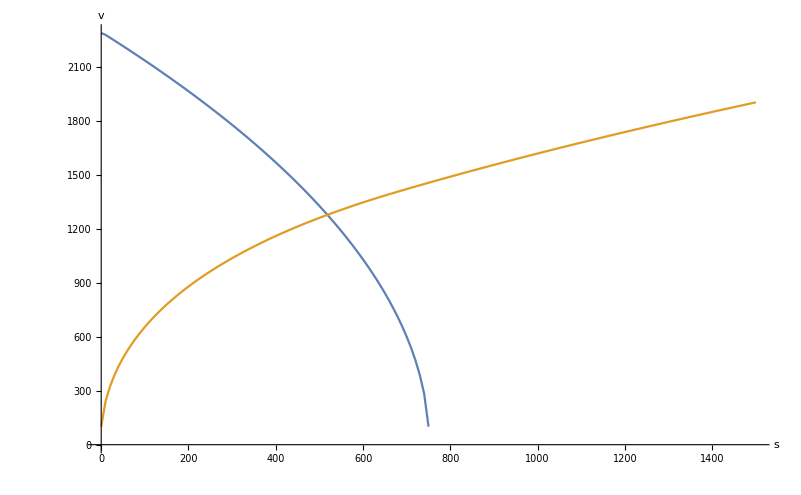

```mathematica
distances2 = Table[i, {i, 0, 1500, 10}];
curvatures2 = Table[0, {i, 0, 1500, 10}];
speeds2 = SpeedPlan[Reverse[distances2], curvatures2, 100, 2300][[1]];

distances1 = Table[i, {i, 0, 750, 10}];
curvatures1 = Table[0, {i, 0, 750, 10}];
speeds1 = SpeedPlan[Reverse[distances1], curvatures1, 2300, 100][[1]]
ListLinePlot[{
Transpose[{distances1, speeds1}],
Transpose[{distances2, speeds2}]
}, AxesLabel->{"s", "v"}, LabelStyle->Large]
```

```mathematica
ListPlot[SpeedPlan[Reverse[distances1], curvatures1, 2300, 100][[1]]]
```

```mathematica
speedlimits
```

{{0.,1294.65},{9.25019,1291.39},{18.4487,1289.02},{27.5984,1287.55},{36.702,1286.98},{45.7622,1287.31},{54.7817,1288.53},187,{1520.77,2171.83},{1532.23,2287.97},{1543.91,2300.},{1555.82,2300.},{1567.96,2300.},{1580.34,2300.},{1592.95,2300.}}
 |  |  |  |

```mathematica
tmp1 = Table[s[1]-s[t], {t, 0, 1, 0.005}];
```

```mathematica
tmp2 = Table[κ[t], {t, 0, 1, 0.005}];
```

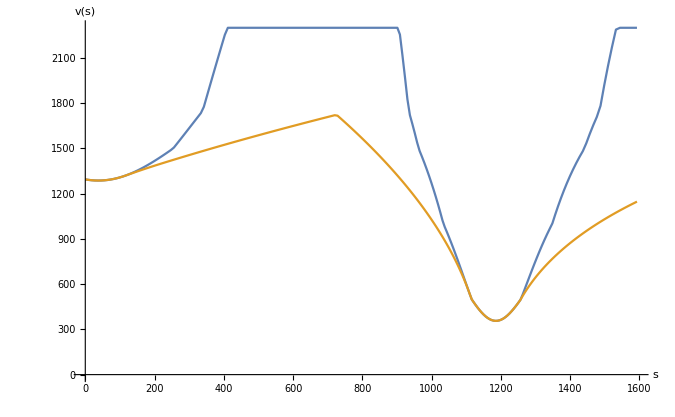

```mathematica
ListLinePlot[{
speedlimits,
Transpose[{s[1] - tmp1, SpeedPlan[tmp1, tmp2, 2300, 2300][[1]]}]
}, AxesLabel->{"s", "v(s)"}, LabelStyle->Large]
```

0.75

0.05

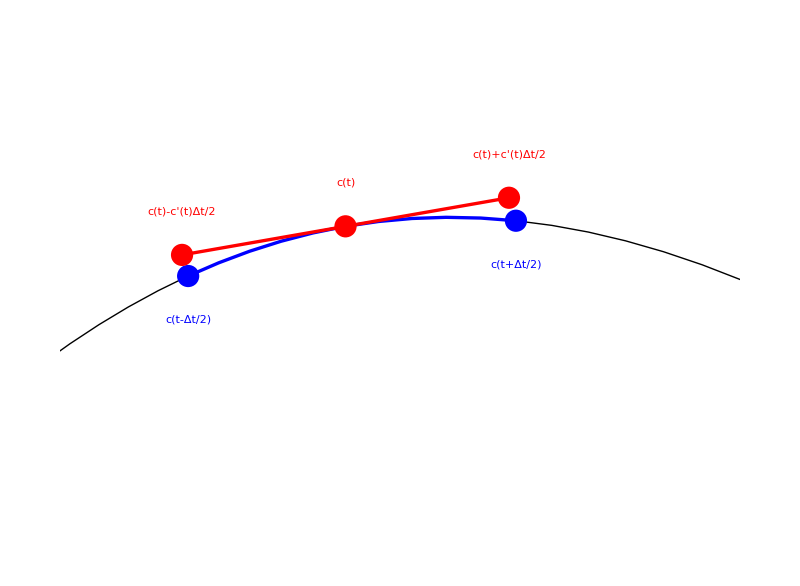

```mathematica
τ = 0.75
Δτ = 0.05
Graphics[{
PointSize[0.02],
Black,
Line[Table[g[t], {t, 0, 1, 0.01}]],
Thickness[0.003],
Blue,
Line[Table[g[t], {t, τ-Δτ, τ+Δτ, 0.01}]],
Point[g[τ+Δτ]],
Text[Style["c(t+Δt/2)",Large],g[τ+Δτ] - scale{0, 0.05}],
Point[g[τ-Δτ]],
Text[Style["c(t-Δt/2)",Large],g[τ-Δτ] - scale{0, 0.05}],

Red,
Point[g[τ]],
Text[Style["c(t)",Large],g[τ] + scale{0, 0.05}],
Point[g[τ] -Δτ g'[τ]],
Text[Style["c(t)-c'(t)Δt/2",Large],g[τ] -Δτ g'[τ] + scale{0, 0.05}],
Point[g[τ] +Δτ g'[τ]],
Text[Style["c(t)+c'(t)Δt/2",Large],g[τ] +Δτ g'[τ] + scale{0, 0.05}],
Line[{g[τ] -Δτ g'[τ], g[τ] +Δτ g'[τ]}]
}, PlotRange->scale{{2.5,3.25}, {2.25,2.8}}, ImageSize->800]
```